## Cross Section Dimensionality

I’m going to do things in SI units here, even though for nuclear physics that’s not the best set of units (natural units are). But the concepts are the same. First step is to get the reduced mass of an α ^235U system.

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[m, α]]
```

```mathematica
Symbolize[Subscript[m, U]]
```

```mathematica
Subscript[m, α] = Quantity[6.64*^-27,"Kilograms"]
```

6.64×10^-27 kg

```mathematica
u = Quantity[1.66*^-27,"Kilograms"]
```

1.66×10^-27 kg

```mathematica
Subscript[m, U] = 235.04*u
```

3.90166×10^-25 kg

```mathematica
μ = Subscript[m, α]*Subscript[m, U]/(Subscript[m, α] + Subscript[m, U])
```

6.52889×10^-27 kg

got the reduced mass μ, now we can try to construct the denominator of the integral on pg 364 or 365, given a specific impact parameter, and initial kinetic energy T_0. Actually, the form on pg 365 is better because the denominator was divided by a factor of the initial kinetic energy.

```mathematica
Symbolize[Subscript[R, U]]
```

```mathematica
Subscript[R, U] = Quantity[7.4*^-15,"Meters"]
```

7.4×10^-15 m

```mathematica
b = 10*Subscript[R, U]
```

7.4×10^-14 m

```mathematica
Symbolize[Subscript[T, 0]]
```

```mathematica
Subscript[T, 0] = UnitConvert[Quantity[1*^6,"eV"],"Joules"]
```

801088317/5000000000000000000000 J

```mathematica
k = Quantity[8.98755*^9,"Newtons"*"Meters"^2/"Coulombs"^2]
```

8.98755×10^9 m^2 N/C^2

```mathematica
Symbolize[Subscript[q, α]]
```

```mathematica
Symbolize[Subscript[q, U]]
```

```mathematica
Subscript[q, α] = UnitConvert[Quantity[2,"ElectronCharge"],"Coulombs"]
```

801088317/2500000000000000000000000000 C

```mathematica
Subscript[q, U] = UnitConvert[Quantity[2,"ElectronCharge"],"Coulombs"]
```

801088317/2500000000000000000000000000 C

```mathematica
U[r_]:=  Subscript[q, α]*Subscript[q, U]*k/Quantity[r,"Meters"]
```

```mathematica
U[QuantityMagnitude@b]
```

1.24707×10^-14 m N

```mathematica
d[r_] = 1- (b^2/Quantity[r,"Meters"]^2) - (U[r]/Subscript[T, 0])
```

1-(5.476×10^-27)/r^2-(5.75986×10^-15)/r

```mathematica
d[1*QuantityMagnitude@b]
```

-0.0778359

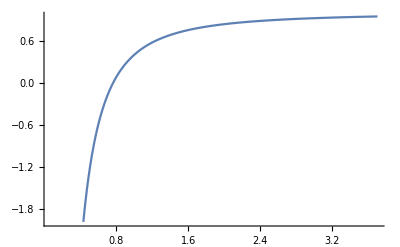

```mathematica
Plot[d[x],{x,0.1*QuantityMagnitude@b,5*QuantityMagnitude@b}]
```

```mathematica
rmin=First[Quantity[FindRoot[d,{0.001*QuantityMagnitude@b,5*QuantityMagnitude@b}],"Meters"]/b]
```

1.03967

```mathematica
g[r_]:= (b/Quantity[r,"Meters"]^2)/Sqrt[d[r]]
```

```mathematica
g[3*QuantityMagnitude@b]
```

1.61635×10^12 per meter

```mathematica
θ= Integrate[Quantity[1,"Meters"]*g[x],{x,rmin*QuantityMagnitude@b,Infinity}]
```

1.5319

```mathematica
Symbolize[Subscript[θ, 2]]
```

```mathematica
Symbolize[Subscript[θ, 1]]
```

```mathematica
Subscript[θ, 1][r_]:= θ= Integrate[Quantity[1,"Meters"]*g[x],{x,rmin*QuantityMagnitude@b,r}]
```

```mathematica
Subscript[θ, 1][r]
```

ConditionalExpression[7.4×10^-14 (2.12269×10^13+(1.35135×10^13 (7.69928×10^-28+1. r) √((-5.476×10^-27-5.75986×10^-15 r+1. r^2)/((7.69928×10^-28+1. r)^2)) ArcTan[(-7.4×10^-14-0.038918 r)/(√(-5.476×10^-27-5.75986×10^-15 r+1. r^2))])/(√(-5.476×10^-27-5.75986×10^-15 r+1. r^2))), ]

```mathematica
ConditionalExpression[1.48*^-14 (1.0613484784848567*^14+(6.75675675675669*^13 (1.7986028639039249*^-28+1. r) √((-2.1904000000000544*^-28-5.7598570427623765*^-15 r+1. r^2)/((1.7986028639039249*^-28+1. r)^2)) ArcTan[(-1.4800000000000035*^-14-0.19458976495819666 r)/(√(-2.1904000000000105*^-28-5.759857042762261*^-15 r+0.99999999999998 r^2))])/(√(-2.1904000000000105*^-28-5.759857042762261*^-15 r+0.99999999999998 r^2))), (1.1479437019748901*^-41+289. Im[r]^2-5.684341886080802*^-14 Re[r]^2)/(17.-9.46678215242772*^14 Re[r])==0||Re[r]>1.79575274114028441599627111173648209627253011`20.35252977886304*^-14||(-1.1479437019748901*^-41-289. Im[r]^2+5.684341886080802*^-14 Re[r]^2)/((17.-9.46678215242772*^14 Re[r])^2)≥0]
```

ConditionalExpression[1.48×10^-14 (1.06135×10^14+(6.75676×10^13 (1.7986×10^-28+1. r) √((-2.1904×10^-28-5.75986×10^-15 r+1. r^2)/((1.7986×10^-28+1. r)^2)) ArcTan[(-1.48×10^-14-0.19459 r)/(√(-2.1904×10^-28-5.75986×10^-15 r+1. r^2))])/(√(-2.1904×10^-28-5.75986×10^-15 r+1. r^2))), ]

```mathematica
Subscript[θ, 1][1.5rmin*QuantityMagnitude@b]
```

0.823537

```mathematica
r:= InverseFunction[Subscript[θ, 1]]
```

```mathematica
Symbolize[Subscript[θ, min]]
```

```mathematica
Subscript[θ, min] = ArcSin[b/(rmin*b)]
```

1.29365

```mathematica
θ1[r_]:=Pi-( Subscript[θ, min] +  Integrate[Quantity[1,"Meters"]*g[x],{x,rmin*QuantityMagnitude@b,r}])
```

```mathematica
Subscript[θ, min]
```

1.29365

```mathematica
θ1[1*rmin*QuantityMagnitude@b]
```

1.84795

```mathematica
invthet = Interpolation[Table[{θ1[r],r},{r,rmin*QuantityMagnitude@b,100*QuantityMagnitude@b,QuantityMagnitude@b}]]
```

InterpolatingFunction[…]

```mathematica
Quantity[invthet[1.9],"Meters"]/b
```

InterpolatingFunction::dmval: Input value {1.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.175875

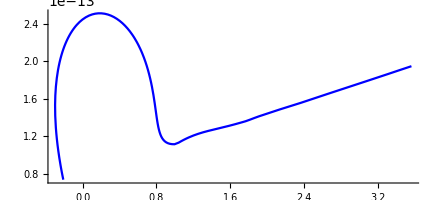

```mathematica
curve =PolarPlot[invthet[x],{x,0.5,π-Subscript[θ, min]},PlotStyle->{Blue,Dashing[None]}]
```

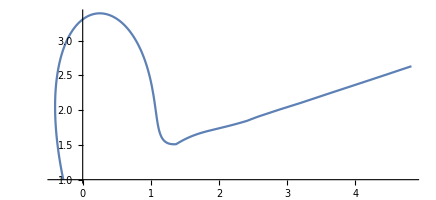

```mathematica
ParametricPlot[{invthet[thet]/(QuantityMagnitude@b)*Cos[thet],invthet[thet]/(QuantityMagnitude@b)*Sin[thet]},{thet,Pi-Subscript[θ, min],0.5}]
```

```mathematica
invthet[Pi-Subscript[θ, min]]/QuantityMagnitude@b
```

1.03967

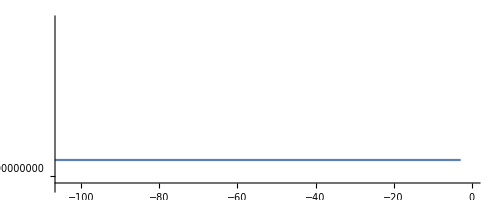

```mathematica
ParametricPlot[{((b/Subscript[R, U])/Sin[Pi-thet])*Cos[thet],((b/Subscript[R, U])/Sin[Pi-thet])*Sin[thet]},{thet,Pi,Pi-Subscript[θ, min]}]
```